.

```mathematica
sys2 := {D[Rp[t],t]==k1*S*(RT-Rp[t])  - k2*Rp[t]}(*0de*)
```

```mathematica
parm = {k1->1, k2->1 , RT-> 1};(*parameter*)
```

```mathematica
List@@sys2[[1]][[2]]
```

{k1 S (RT-Rp[t]),-k2 Rp[t]}

```mathematica
tmp1 = Cases[List@@sys2[[1]][[2]],n1_ /; If[Length[n1]>1,n1[[1]]==-1]]
```

{-k2 Rp[t]}

```mathematica
deg2 = - Plus@@tmp1(*negative part*)
```

k2 Rp[t]

```mathematica
prod2 = Plus@@Complement[List@@sys2[[1]][[2]],tmp1];(*positive part*)
```

```mathematica
Plot[{(prod2 /. parm) /. S->1,(prod2 /. parm) /. S->2,(prod2 /. parm) /. S->3, deg2 /. parm},{Rp[t],0,1},Frame->True,PlotRange->{{0,1},{0,2}}, PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},Black},FrameLabel->{"Rp","Rate"}]
```

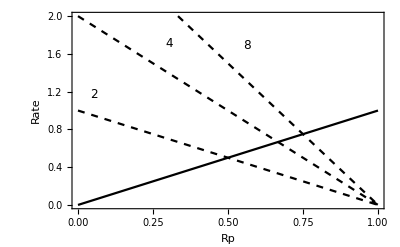

```mathematica
b1=Solve[sys2[[1]][[2]]==0/.parm,Rp[t]];(*nullclines*)
```

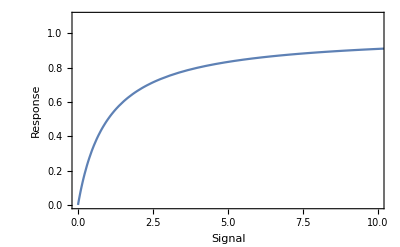

```mathematica
p1=Plot[Evaluate[{Rp[t]/.b1[[1]]}],{S,0,15},PlotRange->{{0,10},{0,1.1}},PlotRangeClipping->True,Frame->True,FrameLabel->{"Signal","Response"}]
```

```mathematica
Show[p1,PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```